```mathematica
eta=0.4883
```

0.4883

```mathematica
epsilon=11/9136
```

11/9136

```mathematica
f[x_]:=(-(eta+epsilon-epsilon*x)+√((eta+epsilon-epsilon*x)^2+4*epsilon*eta*x))/(2x)
```

```mathematica
f[x]
```

(-0.489504+√((0.489504-(11 x)/9136)^2+0.00235171 x)+(11 x)/9136)/(2 x)

```mathematica
p1=Plot[f[x],{x,0,20},PlotRange->PlotRange->{{0,30}{0,0.00005}}]
```

Syntax::bktmcp: Expression "{{0,30}{0,0.00005}" has no closing "}".

```mathematica
f[x]
```

(-0.489504+√((0.489504-(11 x)/9136)^2+0.00235171 x)+(11 x)/9136)/(2 x)

```mathematica
g[x_]:=epsilon*(1-1/x)
```

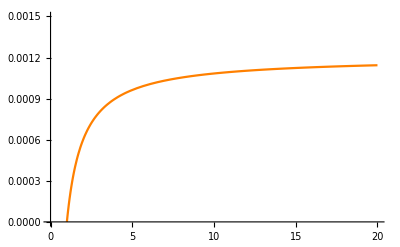

```mathematica
p2=Plot[g[x],{x,0,20},PlotRange->{{0,30}{0,0.00005}},PlotStyle->Orange]
```

```mathematica
h[x_]:=f[x]/g[x]
```

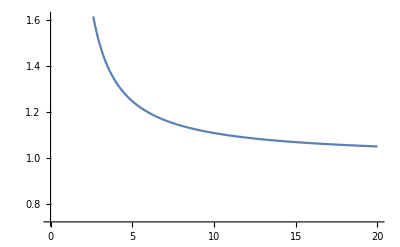

```mathematica
p3=Plot[h[x],{x,0,20}]
```

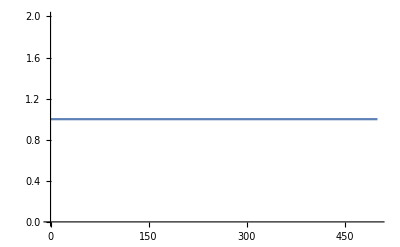

```mathematica
p4=Plot[1,{x,0,500}]
```

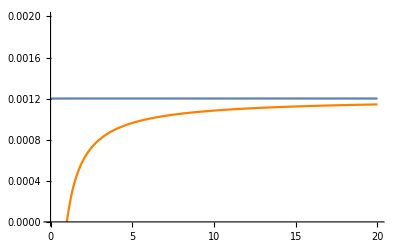

```mathematica
Show[p1,p2]
```

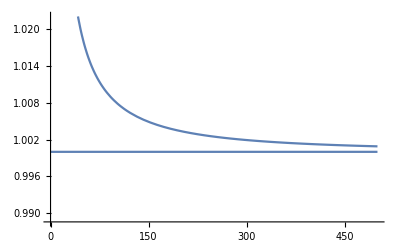

```mathematica
Show[p3,p4]
```